```mathematica
SetDirectory[NotebookDirectory[]];
$HistoryLength=2
```

2

## Demo

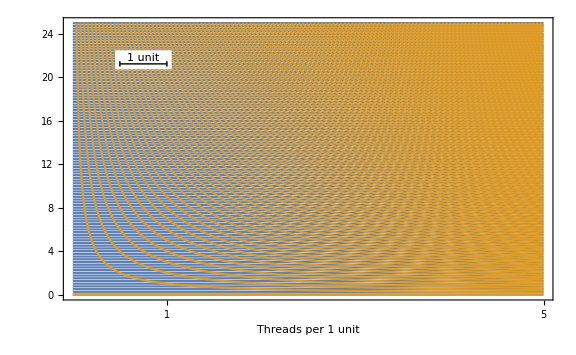

```mathematica
d=1/4.;
a=2.;

xmin=0;
xmax=10;
ymax=25;

Plot[
{
Table[j d,{j,0,ymax/d}],
Table[a k/x,{k,0,ymax xmax/a}](*,
Table[Abs[(a (Δ+0.5))/(x-a/d)],{Δ,0,5}]*)
}
,
{x,0,10},
ImageSize->Large,
PlotRange->{{xmin,xmax},{0,ymax}},
FrameTicks->{Table[{tpu a,tpu},{tpu,1,30}],None},
Frame->True,
FrameLabel->{"Threads per 1 unit",None},
Epilog->{
{White,Rectangle[{xmin+(xmax-xmin)0.09,0.83ymax},{xmin+1+(xmax-xmin)0.11,0.9ymax}]},
Line[{{xmin+(xmax-xmin)0.1,0.85ymax},{xmin+1+(xmax-xmin)0.1,0.85ymax}}],
Line[{{xmin+(xmax-xmin)0.1,0.84ymax},{xmin+(xmax-xmin)0.1,0.86ymax}}],
Line[{{xmin+(xmax-xmin)0.1+1,0.84ymax},{xmin+(xmax-xmin)0.1+1,0.86ymax}}],
Text["1 unit",{xmin+(xmax-xmin)0.1+0.5,0.87ymax}]
}
]
```

```mathematica
2.54/2400
```

0.00105833

```mathematica
1/%
```

944.882

## Fabric

```mathematica
fabric[tpcm_:16,l_:10,h_:5]:=Module[
{
f=0.5,
(*tpcm=10.,*)
d,

xmin=0,xmax=10,
ymin=0,ymax=5
}
,
d=1/tpcm;

Graphics[
{
{
{
Black,
Table[Rectangle[{xmin,(j-f/2) d+ymin},{xmax,(j+f/2) d+ymin}],{j,0,(ymax-ymin)/d}]
},
{
{White,Rectangle[{xmin+(xmax-xmin)0.09,0.83ymax},{xmin+1+(xmax-xmin)0.11,0.9ymax}]},
Thick,
Line[{{xmin+(xmax-xmin)0.1,0.85ymax},{xmin+1+(xmax-xmin)0.1,0.85ymax}}],
Line[{{xmin+(xmax-xmin)0.1,0.84ymax},{xmin+(xmax-xmin)0.1,0.86ymax}}],
Line[{{xmin+(xmax-xmin)0.1+1,0.84ymax},{xmin+(xmax-xmin)0.1+1,0.86ymax}}],
Style[Text["1 cm",{xmin+(xmax-xmin)0.1+0.5,0.87ymax}],FontSize->25,Bold]
}
}
}
,
PlotRange->{{xmin,xmax},{ymin,ymax}},
ImageSize->{1920,1080},
PlotLabel->StringRiffle[ToString/@{"Fabric.",tpcm,"threads per cm.",l,"by",h,"cm"}],
BaseStyle->{FontSize->30,FontFamily->"Courier"}
]
]
```

## Overlay

```mathematica
overlay[tpcmMin_:1,tpcmMax_:30,l_:10,h_:5]:=Module[
{
f=0.5,

(*l=10,h=5,*)

xmin,xmax,
ymin,ymax,

(*tpcmMin=10,tpcmMax=30,*)
a,

ns=500,dx
}
,
dx=l/ns;
a=l/(tpcmMax-tpcmMin);
xmin=a tpcmMin;xmax=xmin+l;
ymin=0;ymax=h;

Graphics[
{
{
{
Black,
Table[
Polygon[Table[{x,(a k)/x+a/(4x)},{x,Max[(a k)/h,xmin]+dx,xmax-dx,dx}]~Join~Table[{x,(a k)/x-a/(4x)},{x,xmax-dx,Max[(a k)/h,xmin]+dx,-dx}]]
,
{k,1,h tpcmMax}
]
}
}
}
,
PlotRange->{{xmin,xmax},{ymin,ymax}},
ImageSize->15000Normalize[{l,h}](*{3840,2160}*)(*{1920,1080}*),
Frame->True,
FrameTicks->{Table[{tpcm a,tpcm,{0,0.008},Directive[Thick]},{tpcm,tpcmMin,tpcmMax}],None},
FrameLabel->{{None,None},{None,
StringRiffle[ToString/@{"Moire thread counter.",tpcmMin,"-",tpcmMax,"threads per cm.",l,"by",h,"cm"}]
}},
BaseStyle->{FontSize->30,FontFamily->"Courier"}
]
];


exportOverlay[tpcmMin_:1,tpcmMax_:30,l_:10,h_:5]:=Export[
StringRiffle[ToString/@{"overlay(",tpcmMin,"-",tpcmMax,")(",l,"-",h,").tiff"},""]
,
overlay[tpcmMin,tpcmMax,l,h]]
```

```mathematica
exportOverlay[1,40,20,7]
```

overlay(1-40)(20-7).tiff

```mathematica
exportOverlay[20,100,20,7]
```

overlay(20-100)(20-7).tiff